# A Robust Solution of Similarity Transformation via Dual Quaternions

Béla Paláncz
Department of Photogrammetry and Geoinformatics
Budapest University of Technology and Economics, H- 1521, Hungary
e-mail: palancz@epito.bme.hu

#### Abstract

A RANSAC type method with a core algorithm based on dual quaternions is presented for similarity transformation. Although dual - quaternion technique basically represents rigid transformation - rotation and translation, -  introducing a simple additional  transformation for the scale parameter, one can successfully use it for similarity transformation too, where scaling is also important. For 3-point problem a determined multivariate polynomial system with 7 unknowns can be developed and easily solved by numerical Groebner basis. Since this computation is fast, it can be efficiently integrated it into a RANSAC type method as a core algorithm, where it is solved repeatedly. For n-point problem we employ Gauss-Jacobi method solving the 3-point subsystem simultaneously.
This contribution will guide the reader through the different  phases of the development of the method step by step illustrated by numerical examples. Finally, example with real world data representing an overdetermined n-point problem is solved. All symbolic and numeric computations have been carried out with Mathematica 10.

#### Keywords

Dual- quaternions, similarity transformation, RANSAC, numerical Groebner basis, Gauss-Jacobi solution

## 1- Introduction

RANSAC is one of the most proper methods to carry out robust parameter estimation, see i.e. Zuliani  (2012) and  Yaniv  (2010). In order to use this method efficiently, one needs a fast core algorithm integrated into RANSAC, which solves the actual subsystems of  an n-point overdetermined system, repeatedly. The efficiency of the RANSAC method can be improved to parallelize the repetitive solution of the subsystems.
To solve such nonlinear  determined subsystems -usually 3-point problems in case of similarity transformation one can use local methods (linearization or  iterative solution), but these require initial values for the parameters, which are rarely are available, see Sjöberg (2013). There are also exist standard non-iterative solutions like Procrustes solution employing SVD see. Awange et al. (2010), or need  tedious algebraic preprocessing, see Paláncz and Zaletnyik (2011).
In this study we introduce dual-quaternions for solving such subsystems in non-iterative way. We have to mention that dual quaternions have been successfully applied already to non-robust similarity transform, see Proskova (2011) or more recently Wang et al (2014) using global numerical optimization techniques.

 Dual numbers are akin to complex numbers and application dual number theory led to dual quaternions, which allows the unification of translation and rotation. In this way a rigid transformation - a rotation about an axis followed by a translation in the direction of this axis - can be represented by dual quaternions, see i.e. Kenwright (2012).

The inverse problem of the rigid transformation means to find the parameters of the transformation when corresponding data pairs are known. This problem which is equivalent to computing the components of the dual quaternion representing the transformation, leads to solving a multivariate polynomial system. 

It can be done without iteration by using numerical Groebner basis, which is a fast, global method. In practice the utilization of this technique is two-folded. One can employ it in non-robust case using Gauss-Jacobi combinatorial technique see i.e. Awange et al (2010) or in robust case as a core algorithm of a robust shell method, like RANSAC.  In this study we concentrate on the robust application.

The structure of this presentation is the following: in Section 2, we introduce quaternions and they application to rigid rotation. Here we also give the matrix equivalent of quaternions as well as illustrate the inverse problem, namely the parameter estimation of the quaternions. In Section 3, the dual quaternions are introduced and their application to rigid transformation -rotation and translation- is demonstrated. In this section we solve the inverse problem for the rigid transformation, too. In Section 4, employing a simple transformation method for scale parameter, we extend the application of dual-quaternions to similarity transformation where scaling is important. The inverse problem of similarity transformation is again illustrated. In Section 5, we introduce the RANSAC method with this extended dual quaternion algorithm as its core algorithm, and illustrate the application with real-word data.

## 2- Quaternion algebra

### 2- 1- Definition of quaternion

Quaternions can be considered as an extension of the complex numbers, namely

Q 
= (q0, q1, q2, q3) = q0 + i q1 + J q2 + K q3 = (q0, q)

where q0 is a scalar real part and  q = (q1, q2, q3) is an imaginary vector. In Mathematica we can work with quaternions as a special data type:

```mathematica
<<Quaternions`
```

Example 1. Let us define a quaternion with the following values for its component,

```mathematica
q0=1;q1=2;q2=3;q3=4;
```

Then the quaternion type variable Q with theses data is

```mathematica
Q=Quaternion[q0,q1,q2,q3]
```

Quaternion[1,2,3,4]

indeed Q is quaternion data type

```mathematica
Head[Q]
```

Quaternion

### 2- 2- Quaternion of rotation

Given an angle θ and the axis of rotation represented by a unit-vector n = (n_x, n_y, n_z). Then we can construct a quaternion as

Q = (cos (θ/2), n sin(θ/2))

or

q0 = cos (θ/2), q1= n_x sin(θ/2), q2= n_y sin(θ/2), q3= n_z sin(θ/2)

Sometimes having the quaternion, we need to know the angle, then

θ =2 Arccos(q0)

and the vector of rotation axis is

n_x= q1/(sin(θ/2)), n_y= q2/(sin(θ/2)), n_z= q3/(sin(θ/2)),

Example 2. Let us develop the quaternion of rotation when  θ = π/4 and the axis of rotation is  n = ( 1/(√3),1/(√3), 1/(√3)).

```mathematica
θ=π/4;n={1/(√3),1/(√3),1/(√3)};
```

where n is a unit vector. Indeed

```mathematica
Norm[n]
```

1

The corresponding quaternion is

```mathematica
Q=Quaternion[Cos[θ/2],Sin[θ/2]n[[1]],Sin[θ/2]n[[2]],Sin[θ/2]n[[3]]]
```

Quaternion[Cos[π/8],Sin[π/8]/(√3),Sin[π/8]/(√3),Sin[π/8]/(√3)]

Using built-in function, we can get the elements of the quaternion, since

```mathematica
wxyz=FromQuaternion[Q]
```

Cos[π/8]+(ⅈ Sin[π/8])/(√3)+(J Sin[π/8])/(√3)+(K Sin[π/8])/(√3)

Then the angel of the rotation is

```mathematica
θ=2ArcCos[Re[wxyz]/.{J->0,K->0}]
```

π/4

or more directly

```mathematica
2ArcCos[Re[Q]]
```

π/4

and the unit vector of the rotation axis is

```mathematica
n={Im[wxyz/.{J->0,K->0}],Coefficient[wxyz,J],Coefficient[wxyz,K]}/Sin[θ/2]
```

{1/(√3),1/(√3),1/(√3)}

The norm of the quaternion is,

```mathematica
Norm[Q]//TrigReduce
```

1

### 2- 3- Rotation transformation with quaternion

Let p a position vector of a point in 3D. We can rotate this vector counter-clockwise with the quaternion of rotation Q as

P_Q= Q P Q_c

where P is a pure quaternion, P = (0, p) and Q_c is the conjugate quaternion of Q. P_Q is quaternion of the rotated vector, which is also a pure quaternion P_Q = (0, p_Q ) and p_Q is the position vector of the rotated point.

Example 3. Let us compute the conjugate of the quaternion of rotation Q . We can use built in function,

```mathematica
Qc=Conjugate[Q]
```

Quaternion[Cos[π/8],-Sin[π/8]/(√3),-Sin[π/8]/(√3),-Sin[π/8]/(√3)]

You can realize that, similarly to complex numbers, the conjugate can be expressed as

Q_c = ( q0
-q1
-q2
-q3)

We can consider the conjugate of a quaternion as the inverse of the quaternion,

```mathematica
FromQuaternion[Q**Qc]
```

1

Example 4. Let a position  vector be p = {2, 0, 1}, which is rotated by  θ = π/2 about the axis given by the vector n . Let us compute the image of p.

```mathematica
p={2,0,1};
```

```mathematica
P=Quaternion[0,p[[1]],p[[2]],p[[3]]]
```

Quaternion[0,2,0,1]

Then according to Eq.(6)

```mathematica
PQ=Q**P**Qc
```

Quaternion[0,1+1/(√6)+Cos[π/8]^2-Sin[π/8]^2,1+1/(√6)-Cos[π/8]^2+Sin[π/8]^2,1-√(2/3)]

The result is a pure quaternion

```mathematica
wxyz=FromQuaternion[PQ]//TrigReduce
```

1/6 (6 ⅈ+3 ⅈ √2+ⅈ √6+6 J-3 √2 J+√6 J+6 K-2 √6 K)

which means its real part is zero. The rotated vector, the vector of the image point is

```mathematica
pQ={Im[wxyz/.{J->0,K->0}],Coefficient[wxyz,J],Coefficient[wxyz,K]}//Simplify
```

{1+1/(√2)+1/(√6),1-1/(√2)+1/(√6),1-√(2/3)}

Let us check the result employing built in function of the Mathematica. The matrix of the rotation is

```mathematica
R=RotationTransform[θ,n]
```

TransformationFunction[(1/3 (1+√2) | 1/6 (2-√2-√6) | 1/6 (2-√2+√6) | 0
1/6 (2-√2+√6) | 1/3 (1+√2) | 1/6 (2-√2-√6) | 0
1/6 (2-√2-√6) | 1/6 (2-√2+√6) | 1/3 (1+√2) | 0
0 | 0 | 0 | 1)]

Then the rotated vector

```mathematica
R[p]//Simplify
```

{1+1/(√2)+1/(√6),1-1/(√2)+1/(√6),1-√(2/3)}

### 2- 4- Quaternion to matrix

In order to avoid using quaternion as a new data type, we can employ the matrix form of a quaternion. A quaternion can be expressed by a 4 × 4 matrix,

Q =(q0, q1, q2, q3)= (q0 | -q1 | -q2 |  -q3
q1 |     q0 | -q3 |      q2
q2 |    q3 |     q0 | -q1
q3 | -q2 |     q1 |     q0)

Let us define a new function, which creates the matrix form of a quaternion from its components,

```mathematica
QuaternionMatrixForm[{q0_,q1_,q2_,q3_}]:={{q0,-q1,-q2,-q3},{q1,q0,-q3,q2},{q2,q3,q0,-q1},{q3,-q2,q1,q0}}
```

Example 5. Do carry out the multiplication P_Q=Q**P**Q_c in matrix form! We should create the matrix form of the quaternions Q and P, namely M_Q and M_P, and the vector form of  Q_c. Then the vector form of the rotated vector  is a pure quaternion

p_Q= M_Q M_P  Q_c= M_Q M_P (    q0
-q1
-q2
-q3)=(0
p_Q1
p_Q2
p_Q3)

Consequently the rotated vector is

p_r=(p_r1
P_r2
P_r3)= (p_Q1
P_Q2
P_Q3)

Let us construct the matrix form of the rotation quaternion, M_Q. Since

```mathematica
wxyz=FromQuaternion[Q]
```

Cos[π/8]+(ⅈ Sin[π/8])/(√3)+(J Sin[π/8])/(√3)+(K Sin[π/8])/(√3)

and

```mathematica
n={Im[wxyz/.{J->0,K->0}],Coefficient[wxyz,J],Coefficient[wxyz,K]}
```

{Sin[π/8]/(√3),Sin[π/8]/(√3),Sin[π/8]/(√3)}

Therefore the matrix form of Q is,

```mathematica
MQ=QuaternionMatrixForm[Join[{Re[wxyz/.{J->0,K->0}]},n]]
```

{{Cos[π/8],-Sin[π/8]/(√3),-Sin[π/8]/(√3),-Sin[π/8]/(√3)},{Sin[π/8]/(√3),Cos[π/8],-Sin[π/8]/(√3),Sin[π/8]/(√3)},{Sin[π/8]/(√3),Sin[π/8]/(√3),Cos[π/8],-Sin[π/8]/(√3)},{Sin[π/8]/(√3),-Sin[π/8]/(√3),Sin[π/8]/(√3),Cos[π/8]}}

or

```mathematica
MatrixForm[MQ]
```

(Cos[π/8] | -Sin[π/8]/(√3) | -Sin[π/8]/(√3) | -Sin[π/8]/(√3)
Sin[π/8]/(√3) | Cos[π/8] | -Sin[π/8]/(√3) | Sin[π/8]/(√3)
Sin[π/8]/(√3) | Sin[π/8]/(√3) | Cos[π/8] | -Sin[π/8]/(√3)
Sin[π/8]/(√3) | -Sin[π/8]/(√3) | Sin[π/8]/(√3) | Cos[π/8])

Similarly, the matrix form of the position vector M_P can be computed as

```mathematica
wxyz=FromQuaternion[P]
```

2 ⅈ+K

and

```mathematica
n={Im[wxyz/.{J->0,K->0}],Coefficient[wxyz,J],Coefficient[wxyz,K]}
```

{2,0,1}

Then

```mathematica
MP=QuaternionMatrixForm[Join[{Re[wxyz/.{J->0,K->0}]},n]];
```

```mathematica
MatrixForm[MP]
```

(0 | -2 | 0 | -1
2 | 0 | -1 | 0
0 | 1 | 0 | -2
1 | 0 | 2 | 0)

or in more simple  way,

```mathematica
QuaternionMatrixForm[{0,2,0,1}]//MatrixForm
```

(0 | -2 | 0 | -1
2 | 0 | -1 | 0
0 | 1 | 0 | -2
1 | 0 | 2 | 0)

The matrix  (vector) form of the conjugate of the rotation quaternion, M_Q can be similarly computed

```mathematica
wxyz=FromQuaternion[Qc]
```

Cos[π/8]-(ⅈ Sin[π/8])/(√3)-(J Sin[π/8])/(√3)-(K Sin[π/8])/(√3)

```mathematica
n={Im[wxyz/.{J->0,K->0}],Coefficient[wxyz,J],Coefficient[wxyz,K]}
```

{-Sin[π/8]/(√3),-Sin[π/8]/(√3),-Sin[π/8]/(√3)}

```mathematica
MQc=Join[{Re[wxyz/.{J->0,K->0}]},n];MatrixForm[MQc]
```

(Cos[π/8]
-Sin[π/8]/(√3)
-Sin[π/8]/(√3)
-Sin[π/8]/(√3))

Then the rotated vector, see Eq. (9)

```mathematica
pQ=MQ.MP.MQc//TrigReduce//Expand
```

{0,1+1/(√2)+1/(√6),1-1/(√2)+1/(√6),1-√(2/3)}

It is really a pure quaternion.

### 2- 5- Inverse problem of rotation

Now, we assume that the coordinates of the original points - let us call them as a source points - and the coordinates of their corresponding transformed points - image points- are known and we should like to get the vector of the rotation axis and the angle of the rotation. This means that we are looking for q0, q1, q2 and q3, the components of the quaternion of the rotation. We have seen that the image point of a the rotated source point is a pure quaternion, see Eq.(9)

p_Q= M_Q M_P  Q_c= M_Q M_P (    q0
-q1
-q2
-q3)=(0
p_Q1
p_Q2
p_Q3)

and the position vector of the rotated point is, see Eq. (10)

p_r=(p_r1
p_r2
p_r3)= (p_Q1
p_Q2
p_Q3)

Consequently, these relations between a source and an corresponding image point coordinates provide only 3 equations for the 4 unknowns. So we need 2 points to solve the inverse problem - more precisely, in addition  one more corresponding coordinate pair  is needed. Let us consider the equations from the terms M_Q M_P  Q_c which provide 4 equations,

```mathematica
Clear[q0,q1,q2,q3]
```

```mathematica
eqs=QuaternionMatrixForm[{q0,q1,q2,q3}].QuaternionMatrixForm[{0,p1,p2,p3}].{q0,-q1,-q2,-q3}
```

{-(-p3 q0-p2 q1+p1 q2) q3-q2 (-p2 q0+p3 q1-p1 q3)-q1 (-p1 q0-p3 q2+p2 q3)+q0 (-p1 q1-p2 q2-p3 q3),-q2 (-p3 q0-p2 q1+p1 q2)-q3 (p2 q0-p3 q1+p1 q3)+q0 (p1 q0+p3 q2-p2 q3)-q1 (-p1 q1-p2 q2-p3 q3),-q1 (p3 q0+p2 q1-p1 q2)+q0 (p2 q0-p3 q1+p1 q3)-q3 (-p1 q0-p3 q2+p2 q3)-q2 (-p1 q1-p2 q2-p3 q3),q0 (p3 q0+p2 q1-p1 q2)-q1 (-p2 q0+p3 q1-p1 q3)-q2 (p1 q0+p3 q2-p2 q3)-q3 (-p1 q1-p2 q2-p3 q3)}

But the first one is zero as it is expected,

```mathematica
eqs[[1]]//Simplify
```

0

Therefore we have 3 prototype equations between the source point p = (p1, p2, p3) and its image point p_r = (p_r1, p_r2, p_r3), namely

```mathematica
eq1=eqs[[2]]-pr1
```

-pr1-q2 (-p3 q0-p2 q1+p1 q2)-q3 (p2 q0-p3 q1+p1 q3)+q0 (p1 q0+p3 q2-p2 q3)-q1 (-p1 q1-p2 q2-p3 q3)

```mathematica
eq2=eqs[[3]]-pr2
```

-pr2-q1 (p3 q0+p2 q1-p1 q2)+q0 (p2 q0-p3 q1+p1 q3)-q3 (-p1 q0-p3 q2+p2 q3)-q2 (-p1 q1-p2 q2-p3 q3)

```mathematica
eq3=eqs[[4]]-pr3
```

-pr3+q0 (p3 q0+p2 q1-p1 q2)-q1 (-p2 q0+p3 q1-p1 q3)-q2 (p1 q0+p3 q2-p2 q3)-q3 (-p1 q1-p2 q2-p3 q3)

We have already one data pair, now we consider a second one, see Table 1.

Table 1.

Coordinates of source and image points A and B

Point | p1 | p2 | p3 | pr1 | pr2 | pr3
A | 2 | 0 | 1 | 1+1/(√2)+1/(√6) | 1-1/(√2)+1/(√6) | 1-√(2/3)
B | 1 | 2 | -1 | 1/6 (4+√2-3 √6) | 1/3 (2+2 √2+√6) | 1/6 (4-5 √2+√6)

Let us develop the equations with these numerical data. The data of the 2 corresponding pairs of points  are

```mathematica
dataA={p1->2,p2->0,p3->1,pr1->1+1/(√2)+1/(√6),pr2->1-1/(√2)+1/(√6),pr3->1-√(2/3)};
dataB={p1->1,p2->2,p3->-1,pr1->1/6 (4+√2-3 √6),pr2->1/3 (2+2 √2+√6),pr3->1/6 (4-5 √2+√6)};
```

Then the equations for the first data pair,

```mathematica
{e1,e2,e3}={eq1,eq2,eq3}/.dataA
```

{-1-1/(√2)-1/(√6)+q0 (2 q0+q2)-q2 (-q0+2 q2)-q1 (-2 q1-q3)-q3 (-q1+2 q3),-1+1/(√2)-1/(√6)-q1 (q0-2 q2)-q2 (-2 q1-q3)-(-2 q0-q2) q3+q0 (-q1+2 q3),-1+√(2/3)+q0 (q0-2 q2)-q2 (2 q0+q2)-q1 (q1-2 q3)-(-2 q1-q3) q3}

and from the second data pair we consider only the first coordinates,

```mathematica
{e4}={eq1}/.dataB
```

{1/6 (-4-√2+3 √6)-q2 (q0-2 q1+q2)+q0 (q0-q2-2 q3)-q3 (2 q0+q1+q3)-q1 (-q1-2 q2+q3)}

To compute Q = (q0, q1, q2, q3) this multivariate polynomial system with 4 unknowns should be solved. Let us employ numerical Groebner basis

```mathematica
AbsoluteTiming[sol=NSolve[{e1,e2,e3,e4},{q0,q1,q2,q3}];]
```

{0.078,Null}

The solutions are

```mathematica
sol
```

{{q0→-0.92388,q1→-0.220942,q2→-0.220942,q3→-0.220942},{q0→0.92388,q1→0.220942,q2→0.220942,q3→0.220942},{q0→0.+0.157802 ⅈ,q1→0.+0.269684 ⅈ,q2→0.+0.0201767 ⅈ,q3→0.-0.949717 ⅈ},{q0→0.-0.157802 ⅈ,q1→0.-0.269684 ⅈ,q2→0.-0.0201767 ⅈ,q3→0.+0.949717 ⅈ},{q0→-0.79435,q1→-0.485455,q2→-0.240309,q3→-0.274943},{q0→0.79435,q1→0.485455,q2→0.240309,q3→0.274943},{q0→0.+0.20514 ⅈ,q1→0.+0.302092 ⅈ,q2→0.-0.268513 ⅈ,q3→0.-0.89138 ⅈ},{q0→0.-0.20514 ⅈ,q1→0.-0.302092 ⅈ,q2→0.+0.268513 ⅈ,q3→0.+0.89138 ⅈ}}

Considering the positive real solutions we get for the quaternion components

```mathematica
Q={q0,q1,q2,q3}/.sol[[2]]
```

{0.92388,0.220942,0.220942,0.220942}

Let us check the result

```mathematica
Q-{Cos[π/8],Sin[π/8]/(√3),Sin[π/8]/(√3),Sin[π/8]/(√3)}
```

{-6.66134×10^-16,1.66533×10^-16,-5.55112×10^-16,0.}

The rotation angle and the coordinates of the rotation axis can be easily computed from these components with Eqs. (4) and (5).   Although the standard rotation matrix can be expressed by the element of the quaternion, too,

RQ = (q0^2+q1^2-q2^2-q3^2 | 2 (q1 q2-q0 q3) | 2 (q0 q2+q1 q3)
2 (q1 q2+q0 q3) | q0^2-q1^2+q2^2-q3^2 | 2 (-q0 q1+q2 q3)
2 (-q0 q2+q1 q3) | 2 (q0 q1+q2 q3) | q0^2-q1^2-q2^2+q3^2)

Let us define the corresponding Mathematica  function,

```mathematica
QuaternionToRotationMatrix[{q0_,q1_,q2_,q3_}]:={{q0^2+q1^2-q2^2-q3^2,2(q1 q2-q0 q3),2(q1 q3+q0 q2)},{2(q1 q2+q0 q3),q0^2-q1^2+q2^2-q3^2,2(q2 q3-q0 q1)},{2(q1 q3-q0 q2),2(q2 q3+q0 q1),q0^2-q1^2-q2^2+q3^2}}
```

Then the rotation matrix is

```mathematica
RQ=QuaternionToRotationMatrix[Q];MatrixForm[RQ]
```

(0.804738 | -0.310617 | 0.505879
0.505879 | 0.804738 | -0.310617
-0.310617 | 0.505879 | 0.804738)

To check this result, let us consider the rotation transformation resulted by the built in function of Mathematica. We have seen that the rotation transformation function is

```mathematica
R
```

TransformationFunction[(1/3 (1+√2) | 1/6 (2-√2-√6) | 1/6 (2-√2+√6) | 0
1/6 (2-√2+√6) | 1/3 (1+√2) | 1/6 (2-√2-√6) | 0
1/6 (2-√2-√6) | 1/6 (2-√2+√6) | 1/3 (1+√2) | 0
0 | 0 | 0 | 1)]

Extracting the rotation matrix

```mathematica
RM=Map[Drop[#,-1]&,Drop[R[[1]],-1]];MatrixForm[RM]
```

(1/3 (1+√2) | 1/6 (2-√2-√6) | 1/6 (2-√2+√6)
1/6 (2-√2+√6) | 1/3 (1+√2) | 1/6 (2-√2-√6)
1/6 (2-√2-√6) | 1/6 (2-√2+√6) | 1/3 (1+√2))

and indeed, the dual quaternion solution provide the same result,

```mathematica
MatrixForm[RM-RQ]
```

(1.22125×10^-15 | -5.55112×10^-16 | 7.77156×10^-16
6.66134×10^-16 | 1.44329×10^-15 | 5.55112×10^-17
-7.21645×10^-16 | 3.33067×10^-16 | 1.44329×10^-15)

## 3- Dual quaternions

### 3- 1- Dual number and dual quaternion

Dual numbers were invented by Clifford in 1873. Dual numbers are akin to complex numbers.

z = r + ϵ d   with  ϵ^2= 0   but ϵ ≠ 0

where ϵ is known as the dual operator, r is the real part and d is the dual part of a dual number. Now, let us consider r and d as two standard quaternions, Q and Q_ϵ, then

Q_d= Q + ϵ Q_ϵ

where Q_d is called as dual quaternion and it can be considered as an extension of the dual numbers. This formalism allows the unification of rotation and translation.

### 3- 2- Dual Quaternion to rigid transformation

Let p = (p_1,p_2,p_3) is a position vector of a source point, t = (t_1, t_2, t_3) is a translation vector and Q = (cos (θ/2), n sin(θ/2)) is a unit quaternion for rotation. Then we can express the image of the point p_Q_d= (p_Q_d_1, p_Q_d_2, p_Q_d_3) after this translation and rotation as the dual quaternion of the image point is,

P_Q_d= Q_d P_d Q_d_c

where P_d is a unit dual quaternion

P_d = 1 + ϵ (i p_1  + J p_2+ K p_3)

and let 𝒯 is a pure quaternion as

𝒯=0 +(i t_1  + J t_2+ K t_3)

Now the dual quaternion Q_d has its real part Q and its dual part 1/2 𝒯 Q, namely

Q_d = Q + ϵ Q_ϵ = Q + ϵ 1/2 𝒯 Q

and Q_d_c is the conjugate of  Q_d. The resulted dual quaternion P_Q_d is a unit dual quaternion

P_Q_d=1 + ϵ (p_Q_d_1,p_Q_d_2, p_Q_d_3)

Now let us develop some Mathematical  functions to handle dual quaternions, since Mathematica does not support operations with dual quaternion data type.

• First, we  define a function, which computes dual quaternion from the quaternion of the real part and from the dual part,

```mathematica
DualQuaternion[Q1_,Q2_]:=Quaternion[Q1[[1]],Q1[[2]],Q1[[3]],Q1[[4]]]+e Quaternion[Q2[[1]],Q2[[2]],Q2[[3]],Q2[[4]]]
```

• We require to define the product of two dual quaternions. Let Q_d_1 and Q_d_2 two dual quaternions, where Q_d= Q + ϵ Q_ϵ, then

Q_d_1 Q_d_2 =Q_1 Q_2+ϵ (Q_1 Q_ϵ_2 + Q_ϵ_1 Q_2)

The corresponding Mathematica function is

```mathematica
ProductDual[Q1_,Q2_]:=Coefficient[Q1,e,0]**Coefficient[Q2,e,0]+e(Coefficient[Q1,e,0]**Coefficient[Q2,e,1]+Coefficient[Q1,e,1]**Coefficient[Q2,e,0])
```

• We also need a function, which computes the dual conjugate of the dual quaternion, Q_d_c. The conjugate of the quaternion Q is Q_c, and the dual conjugate of the dual quaternion is

Q_d_c=Q_c-  ϵ Q_ϵ_c

The corresponding Mathematica function is

```mathematica
ConjugateDual[Q_]:=(Conjugate[Coefficient[Q,e,0]]-e Conjugate[Coefficient[Q,e,1]])
```

• We may also require to extract the real and the dual part of a dual quaternion,

```mathematica
RealFromDualQuaternion[Q_]:=FromQuaternion[Coefficient[Q,e,0]]
```

```mathematica
DualFromDualQuaternion[Q_]:=FromQuaternion[Coefficient[Q,e,1]]
```

Example 6. First let us apply dual quaternion to only pure rotation employing data used in the examples above. Since there is no translation, now the pure zero quaternion, namely  𝒯 ≡0.

```mathematica
T=Quaternion[0,0,0,0]
```

Quaternion[0,0,0,0]

Let the rotation represented by

```mathematica
Q=Quaternion[Cos[π/8],Sin[π/8]/(√3),Sin[π/8]/(√3),Sin[π/8]/(√3)];
```

the dual part of the quaternion, see Eq. (19),

```mathematica
Qe=1/2 T**Q
```

Quaternion[0,0,0,0]

Then the dual quaternion  Q_d itself  is

```mathematica
Qd=DualQuaternion[Q,Qe]
```

e Quaternion[0,0,0,0]+Quaternion[Cos[π/8],Sin[π/8]/(√3),Sin[π/8]/(√3),Sin[π/8]/(√3)]

Similarly let us compute the unit dual quaternion of the p vector, namely for P_d

```mathematica
Pd=DualQuaternion[Quaternion[1,0,0,0],P]
```

e Quaternion[0,2,0,1]+Quaternion[1,0,0,0]

Let us compute the dual conjugate of this dual quaternion

```mathematica
Qdc=ConjugateDual[Qd]
```

e Quaternion[0,0,0,0]+Quaternion[Cos[π/8],-Sin[π/8]/(√3),-Sin[π/8]/(√3),-Sin[π/8]/(√3)]

Now, we  can compute the dual quaternion of the 3D rigid transformation, now only rotation P_Q_d= Q_d P_d Q_d_c

```mathematica
PQd=ProductDual[ProductDual[Qd,Pd],Qdc]
```

e Quaternion[0,1+1/(√6)+Cos[π/8]^2-Sin[π/8]^2,1+1/(√6)-Cos[π/8]^2+Sin[π/8]^2,1-√(2/3)]+Quaternion[1,0,0,0]

The real part of the resulted dual quaternion is

```mathematica
wxyz=RealFromDualQuaternion[PQd]
```

1

and the dual part of the resulted dual quaternion is

```mathematica
ewxyz=DualFromDualQuaternion[PQd]//TrigReduce
```

1/6 (6 ⅈ+3 ⅈ √2+ⅈ √6+6 J-3 √2 J+√6 J+6 K-2 √6 K)

Then the rotated vector is

```mathematica
{Im[ewxyz/.{J->0,K->0}],Coefficient[ewxyz,J],Coefficient[ewxyz,K]}//Simplify
```

{1+1/(√2)+1/(√6),1-1/(√2)+1/(√6),1-√(2/3)}

Example 7. Now, we add a translation to the transformation with vector t = (1, 2, -1),

The pure quaternion for translation  𝒯  is

```mathematica
T=Quaternion[0,1,2,-1]
```

Quaternion[0,1,2,-1]

```mathematica
Qe=1/2 T**Q
```

Quaternion[-Sin[π/8]/(√3),1/2 (Cos[π/8]+√3 Sin[π/8]),1/2 (2 Cos[π/8]-(2 Sin[π/8])/(√3)),1/2 (-Cos[π/8]-Sin[π/8]/(√3))]

Then the dual quaternion  Q_d is

```mathematica
Qd=DualQuaternion[Q,Qe]
```

Quaternion[Cos[π/8],Sin[π/8]/(√3),Sin[π/8]/(√3),Sin[π/8]/(√3)]+e Quaternion[-Sin[π/8]/(√3),1/2 (Cos[π/8]+√3 Sin[π/8]),1/2 (2 Cos[π/8]-(2 Sin[π/8])/(√3)),1/2 (-Cos[π/8]-Sin[π/8]/(√3))]

Its dual conjugate

```mathematica
Qdc=ConjugateDual[Qd]
```

Quaternion[Cos[π/8],-Sin[π/8]/(√3),-Sin[π/8]/(√3),-Sin[π/8]/(√3)]+e Quaternion[Sin[π/8]/(√3),1/2 (Cos[π/8]+√3 Sin[π/8]),1/2 (2 Cos[π/8]-(2 Sin[π/8])/(√3)),1/2 (-Cos[π/8]-Sin[π/8]/(√3))]

Now, we  can compute the dual quaternion of the 3D rigid transformation P_Q_d= Q_d P_d Q_d_c , see Eq. (16)

```mathematica
PQd=ProductDual[ProductDual[Qd,Pd],Qdc]
```

e Quaternion[0,2+1/(√2)+1/(√6),3-1/(√2)+1/(√6),-√(2/3)]+Quaternion[1,0,0,0]

and

```mathematica
wxyz=RealFromDualQuaternion[PQd]
```

1

The dual part of the resulted dual quaternion is

```mathematica
ewxyz=DualFromDualQuaternion[PQd]//TrigReduce
```

ⅈ (2+1/(√2)+1/(√6))+(3-1/(√2)+1/(√6)) J-√(2/3) K

Then the image  vector, rotated and translated source vector is

```mathematica
{Im[ewxyz/.{J->0,K->0}],Coefficient[ewxyz,J],Coefficient[ewxyz,K]}//Simplify
```

{2+1/(√2)+1/(√6),3-1/(√2)+1/(√6),-√(2/3)}

Let us check this result via using built-in function of Mathematica The transformation function for this translation is

```mathematica
T=TranslationTransform[{1,2,-1}]
```

TransformationFunction[(1 | 0 | 0 | 1
0 | 1 | 0 | 2
0 | 0 | 1 | -1
0 | 0 | 0 | 1)]

Then the translation after rotation

```mathematica
pT=T[R[p]]//Simplify
```

{2+1/(√2)+1/(√6),3-1/(√2)+1/(√6),-√(2/3)}

So we have the same result.

### 3- 3- Dual quaternion to matrix

Let us consider a dual quaternion as Q_d = Q + ϵ Q_ϵ, where the real part is Q = (q0, q1, q2, q3) and the dual part

Q_ϵ=1/2 𝒯 Q=1/2 (0,t1,t2,t3)**(q0,q1,q2,q3)

then the  matrix representation of  Q_d is a 8 × 8 matrix,

Q_d =(Q | Q_ϵ
0 | Q)

The matrix form of Q is

```mathematica
Q=QuaternionMatrixForm[{q0,q1,q2,q3}];MatrixForm[Q]
```

(q0 | -q1 | -q2 | -q3
q1 | q0 | -q3 | q2
q2 | q3 | q0 | -q1
q3 | -q2 | q1 | q0)

The dual part is

```mathematica
qe=1/2 QuaternionMatrixForm[{0,t1,t2,t3}].{q0,q1,q2,q3};
```

In matrix form

```mathematica
Qe=QuaternionMatrixForm[qe];MatrixForm[Qe]
```

(1/2 (-q1 t1-q2 t2-q3 t3) | 1/2 (-q0 t1-q3 t2+q2 t3) | 1/2 (q3 t1-q0 t2-q1 t3) | 1/2 (-q2 t1+q1 t2-q0 t3)
1/2 (q0 t1+q3 t2-q2 t3) | 1/2 (-q1 t1-q2 t2-q3 t3) | 1/2 (-q2 t1+q1 t2-q0 t3) | 1/2 (-q3 t1+q0 t2+q1 t3)
1/2 (-q3 t1+q0 t2+q1 t3) | 1/2 (q2 t1-q1 t2+q0 t3) | 1/2 (-q1 t1-q2 t2-q3 t3) | 1/2 (-q0 t1-q3 t2+q2 t3)
1/2 (q2 t1-q1 t2+q0 t3) | 1/2 (q3 t1-q0 t2-q1 t3) | 1/2 (q0 t1+q3 t2-q2 t3) | 1/2 (-q1 t1-q2 t2-q3 t3))

Let us put them together in a matrix

```mathematica
MD=Join[Join[Q,Qe,2],Join[{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},Q,2]];MatrixForm[MD]
```

(q0 | -q1 | -q2 | -q3 | 1/2 (-q1 t1-q2 t2-q3 t3) | 1/2 (-q0 t1-q3 t2+q2 t3) | 1/2 (q3 t1-q0 t2-q1 t3) | 1/2 (-q2 t1+q1 t2-q0 t3)
q1 | q0 | -q3 | q2 | 1/2 (q0 t1+q3 t2-q2 t3) | 1/2 (-q1 t1-q2 t2-q3 t3) | 1/2 (-q2 t1+q1 t2-q0 t3) | 1/2 (-q3 t1+q0 t2+q1 t3)
q2 | q3 | q0 | -q1 | 1/2 (-q3 t1+q0 t2+q1 t3) | 1/2 (q2 t1-q1 t2+q0 t3) | 1/2 (-q1 t1-q2 t2-q3 t3) | 1/2 (-q0 t1-q3 t2+q2 t3)
q3 | -q2 | q1 | q0 | 1/2 (q2 t1-q1 t2+q0 t3) | 1/2 (q3 t1-q0 t2-q1 t3) | 1/2 (q0 t1+q3 t2-q2 t3) | 1/2 (-q1 t1-q2 t2-q3 t3)
0 | 0 | 0 | 0 | q0 | -q1 | -q2 | -q3
0 | 0 | 0 | 0 | q1 | q0 | -q3 | q2
0 | 0 | 0 | 0 | q2 | q3 | q0 | -q1
0 | 0 | 0 | 0 | q3 | -q2 | q1 | q0)

Similarly, the matrix representation of the dual conjugate of the dual quaternion is

Q_d_c=(Q_c | -Q_ϵ_c
0 | Q_c)

```mathematica
Qc=QuaternionMatrixForm[{q0,-q1,-q2,-q3}];MatrixForm[Qc]
```

(q0 | q1 | q2 | q3
-q1 | q0 | q3 | -q2
-q2 | -q3 | q0 | q1
-q3 | q2 | -q1 | q0)

```mathematica
Qec=QuaternionMatrixForm[{qe[[1]],-qe[[2]],-qe[[3]],-qe[[4]]}];MatrixForm[Qec]
```

(1/2 (-q1 t1-q2 t2-q3 t3) | 1/2 (q0 t1+q3 t2-q2 t3) | 1/2 (-q3 t1+q0 t2+q1 t3) | 1/2 (q2 t1-q1 t2+q0 t3)
1/2 (-q0 t1-q3 t2+q2 t3) | 1/2 (-q1 t1-q2 t2-q3 t3) | 1/2 (q2 t1-q1 t2+q0 t3) | 1/2 (q3 t1-q0 t2-q1 t3)
1/2 (q3 t1-q0 t2-q1 t3) | 1/2 (-q2 t1+q1 t2-q0 t3) | 1/2 (-q1 t1-q2 t2-q3 t3) | 1/2 (q0 t1+q3 t2-q2 t3)
1/2 (-q2 t1+q1 t2-q0 t3) | 1/2 (-q3 t1+q0 t2+q1 t3) | 1/2 (-q0 t1-q3 t2+q2 t3) | 1/2 (-q1 t1-q2 t2-q3 t3))

Let us put them together

```mathematica
MQc=Join[Join[Qc,-Qec,2],Join[{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},Qc,2]];MatrixForm[MQc]
```

(q0 | q1 | q2 | q3 | 1/2 (q1 t1+q2 t2+q3 t3) | 1/2 (-q0 t1-q3 t2+q2 t3) | 1/2 (q3 t1-q0 t2-q1 t3) | 1/2 (-q2 t1+q1 t2-q0 t3)
-q1 | q0 | q3 | -q2 | 1/2 (q0 t1+q3 t2-q2 t3) | 1/2 (q1 t1+q2 t2+q3 t3) | 1/2 (-q2 t1+q1 t2-q0 t3) | 1/2 (-q3 t1+q0 t2+q1 t3)
-q2 | -q3 | q0 | q1 | 1/2 (-q3 t1+q0 t2+q1 t3) | 1/2 (q2 t1-q1 t2+q0 t3) | 1/2 (q1 t1+q2 t2+q3 t3) | 1/2 (-q0 t1-q3 t2+q2 t3)
-q3 | q2 | -q1 | q0 | 1/2 (q2 t1-q1 t2+q0 t3) | 1/2 (q3 t1-q0 t2-q1 t3) | 1/2 (q0 t1+q3 t2-q2 t3) | 1/2 (q1 t1+q2 t2+q3 t3)
0 | 0 | 0 | 0 | q0 | q1 | q2 | q3
0 | 0 | 0 | 0 | -q1 | q0 | q3 | -q2
0 | 0 | 0 | 0 | -q2 | -q3 | q0 | q1
0 | 0 | 0 | 0 | -q3 | q2 | -q1 | q0)

As we have seen, the dual quaternion of the position vector of the source  point to be transformed is a unit dual quaternion, see Eq. (17)

P_d = 1 + ϵ (i p_1  + J p_2+ K p_3)

Therefore the real part of  P_d is

```mathematica
PdR=QuaternionMatrixForm[{1,0,0,0}];MatrixForm[PdR]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

and its dual part

```mathematica
PdD=QuaternionMatrixForm[{0,p1,p2,p3}];MatrixForm[PdD]
```

(0 | -p1 | -p2 | -p3
p1 | 0 | -p3 | p2
p2 | p3 | 0 | -p1
p3 | -p2 | p1 | 0)

Now putting them together in a matrix

```mathematica
MPd=Join[Join[PdR,PdD,2],Join[{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},PdR,2]];MatrixForm[MPd]
```

(1 | 0 | 0 | 0 | 0 | -p1 | -p2 | -p3
0 | 1 | 0 | 0 | p1 | 0 | -p3 | p2
0 | 0 | 1 | 0 | p2 | p3 | 0 | -p1
0 | 0 | 0 | 1 | p3 | -p2 | p1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

Then the matrix form of the dual quaternion representing the image point is

```mathematica
PQd=MD.MPd.MQc;
```

This matrix can be simplified again considering  q0^2+q1^2+q2^2+q3^2= 1. Indeed

```mathematica
dataQ={q0->Cos[π/8],q1->Sin[π/8]/(√3),q2->Sin[π/8]/(√3),q3->Sin[π/8]/(√3)};
```

```mathematica
((q0^2+q1^2+q2^2+q3^2)/.dataQ)//TrigReduce
```

1

Therefore  P_Qd can be simplified, too

```mathematica
PQd=(PQd//FullSimplify)/.{(q0^2+q1^2+q2^2+q3^2)->1};
```

The result is a unit dual quaternion in matrix form. Let the image point coordinates (p_Q_d_1,p_Q_d_2, p_Q_d_3), and we have seen that the result matrix is the matrix form of  the dual quaternion, see Eq. (20)

P_Q_d=1 + ϵ (p_Q_d_1,p_Q_d_2,p_Q_d_3)

In addition the matrix form of the dual part, which is a pure quaternion is

```mathematica
QuaternionMatrixForm[{0,pQd1,pQd2,pQd3}]//MatrixForm
```

(0 | -pQd1 | -pQd2 | -pQd3
pQd1 | 0 | -pQd3 | pQd2
pQd2 | pQd3 | 0 | -pQd1
pQd3 | -pQd2 | pQd1 | 0)

Therefore the structure of our matrix is

P_Qd=(1 | 0 | 0 | 0 | 0 | -p_Q_d_1 | -p_Q_d_2 | -p_Q_d_3
0 | 1 | 0 | 0 | p_Q_d_1 | 0 | -p_Q_d_3 |   p_Q_d_2
0 | 0 | 1 | 0 | p_Q_d_2 |   p_Q_d_3 | 0 | -p_Q_d_1
0 | 0 | 0 | 1 | p_Q_d_3 | -p_Q_d_2 |   p_Q_d_1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

Indeed,

```mathematica
PQd[[All,1;;4]]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
PQd[[5;;8]]//MatrixForm
```

(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

Then the coordinates of the position of the image  vector are

```mathematica
pQd1=-PQd[[1,6]]
```

2 p2 q1 q2-2 p2 q0 q3+2 p3 (q0 q2+q1 q3)-p1 (-q0^2-q1^2+q2^2+q3^2)+t1

```mathematica
pQd2=-PQd[[1,7]]
```

2 (-p3 q0 q1+p1 q1 q2+p1 q0 q3+p3 q2 q3)-p2 (-q0^2+q1^2-q2^2+q3^2)+t2

```mathematica
pQd3=-PQd[[1,8]]
```

2 (p2 q0 q1-p1 q0 q2+p1 q1 q3+p2 q2 q3)-p3 (-q0^2+q1^2+q2^2-q3^2)+t3

Example 8. Let us compute the coordinates of the image position vector with data used in Example 7, using matrix representation.

The translation vector

```mathematica
datat={t1->1,t2->2,t3->-1};
```

The rotation quaternion

```mathematica
dataQ
```

{q0→Cos[π/8],q1→Sin[π/8]/(√3),q2→Sin[π/8]/(√3),q3→Sin[π/8]/(√3)}

then the coordinates are

```mathematica
{pQd1,pQd2,pQd3}/.dataQ/.datat/.{p1->2,p2->0,p3->1}//TrigReduce//FullSimplify
```

{2+1/(√2)+1/(√6),3-1/(√2)+1/(√6),-√(2/3)}

Let us check it with the result of the Example 7

```mathematica
pT
```

{2+1/(√2)+1/(√6),3-1/(√2)+1/(√6),-√(2/3)}

### 3- 4- Inverse problem of the rigid transformation

The prototype equations describing the relation between the source vector  p = (p_1,p_2, p_3) and the image vector p_Q_d = (p_Q_d_1,p_Q_d_2, p_Q_d_3) with the components of the unit quaternion of rotation Q = (q0, q1 , q2, q3)  and translation vector  t =  (t_1, t_2, t_3) according to the result of the last section, can be written as

```mathematica
Clear[pQd1,pQd2,pQd3];
```

```mathematica
eqPt1=pQd1-(2 p2 q1 q2-2 p2 q0 q3+2 p3 (q0 q2+q1 q3)-p1 (-q0^2-q1^2+q2^2+q3^2)+ t1);
```

```mathematica
eqPt2=pQd2-(2 (-p3 q0 q1+p1 q1 q2+p1 q0 q3+p3 q2 q3)-p2 (-q0^2+q1^2-q2^2+q3^2)+ t2);
```

```mathematica
eqPt3=pQd3-(2 (p2 q0 q1-p1 q0 q2+p1 q1 q3+p2 q2 q3)-p3 (-q0^2+q1^2+q2^2-q3^2)+ t3);
```

Example 9. Do compute the parameters of the rigid transformation determined by Q and t! Since we need to compute the 4 + 3 components, we require 7 equations, which means we should use 3 corresponding points.

The three corresponding data pairs are in Table 2.

Table 2.

Coordinates of source and image points

Point  | p1 | p2 | p3 | pQd1 | pQd2 | pQd3
A | 2 | 0 | 1 | 1+1/(√2)+1/(√6) | 1-1/(√2)+1/(√6) | 1-√(2/3)
B | 1 | 2 | -1 | 1/6 (4+√2-3 √6) | 1/3 (2+2 √2+√6) | 1/6 (4-5 √2+√6)
C | 0 | 1 | 2 | 2-1/(√2)+1/(√6) | 3-√(2/3) | 1/(√2)+1/(√6)

Then our equation system is

```mathematica
dataA={p1->2,p2->0,p3->1,pQd1->2+1/(√2)+1/(√6),pQd2->3-1/(√2)+1/(√6),pQd3->-√(2/3)};
```

```mathematica
{e1,e2,e3}={eqPt1,eqPt2,eqPt3}/.dataA
```

{2+1/(√2)+1/(√6)-2 (q0 q2+q1 q3)+2 (-q0^2-q1^2+q2^2+q3^2)-t1,3-1/(√2)+1/(√6)-2 (-q0 q1+2 q1 q2+2 q0 q3+q2 q3)-t2,-√(2/3)-q0^2+q1^2+q2^2-q3^2-2 (-2 q0 q2+2 q1 q3)-t3}

```mathematica
dataB={p1->1,p2->2,p3->-1,pQd1->1/6 (10+√2-3 √6),pQd2->1/3 (8+2 √2+√6),pQd3->1/6 (-2-5 √2+√6)};
```

```mathematica
{e4,e5,e6}={eqPt1,eqPt2,eqPt3}/.dataB
```

{1/6 (10+√2-3 √6)-q0^2-q1^2-4 q1 q2+q2^2+4 q0 q3+q3^2+2 (q0 q2+q1 q3)-t1,1/3 (8+2 √2+√6)-2 (q0 q1+q1 q2+q0 q3-q2 q3)+2 (-q0^2+q1^2-q2^2+q3^2)-t2,1/6 (-2-5 √2+√6)+q0^2-q1^2-q2^2+q3^2-2 (2 q0 q1-q0 q2+q1 q3+2 q2 q3)-t3}

```mathematica
dataC={p1->0,p2->1,p3->2,pQd1->2-1/(√2)+1/(√6),pQd2->3-√(2/3),pQd3->1/(√2)+1/(√6)};
```

From the third point, we use only the first corresponding coordinates,

```mathematica
{e7}={eqPt1}/.dataC
```

{2-1/(√2)+1/(√6)-2 q1 q2+2 q0 q3-4 (q0 q2+q1 q3)-t1}

These 7 equations can be simplified by eliminating the components of the translation vector t.

```mathematica
E1=e1-e4
```

2+1/(√2)+1/(√6)+1/6 (-10-√2+3 √6)+q0^2+q1^2+4 q1 q2-q2^2-4 q0 q3-q3^2-4 (q0 q2+q1 q3)+2 (-q0^2-q1^2+q2^2+q3^2)

```mathematica
E2=e2-e5
```

3-1/(√2)+1/(√6)+1/3 (-8-2 √2-√6)+2 (q0 q1+q1 q2+q0 q3-q2 q3)-2 (-q0 q1+2 q1 q2+2 q0 q3+q2 q3)-2 (-q0^2+q1^2-q2^2+q3^2)

```mathematica
E3=e3-e6
```

-√(2/3)+1/6 (2+5 √2-√6)-2 q0^2+2 q1^2+2 q2^2-2 q3^2-2 (-2 q0 q2+2 q1 q3)+2 (2 q0 q1-q0 q2+q1 q3+2 q2 q3)

```mathematica
E4=e1-e7
```

√2+2 q1 q2-2 q0 q3+2 (q0 q2+q1 q3)+2 (-q0^2-q1^2+q2^2+q3^2)

```mathematica
AbsoluteTiming[sol=NSolve[{E1,E2,E3,E4},{q0,q1,q2,q3}];]
```

{0.078,Null}

```mathematica
sol
```

{{q0→0.+0.374952 ⅈ,q1→0.-0.460133 ⅈ,q2→0.-0.684527 ⅈ,q3→0.-0.423215 ⅈ},{q0→0.-0.374952 ⅈ,q1→0.+0.460133 ⅈ,q2→0.+0.684527 ⅈ,q3→0.+0.423215 ⅈ},{q0→0.92388,q1→0.220942,q2→0.220942,q3→0.220942},{q0→-0.92388,q1→-0.220942,q2→-0.220942,q3→-0.220942},{q0→0.529865,q1→0.605749,q2→-0.392324,q3→0.445413},{q0→-0.529865,q1→-0.605749,q2→0.392324,q3→-0.445413},{q0→0.-0.254221 ⅈ,q1→0.-0.181667 ⅈ,q2→0.+0.369637 ⅈ,q3→0.+0.875064 ⅈ},{q0→0.+0.254221 ⅈ,q1→0.+0.181667 ⅈ,q2→0.-0.369637 ⅈ,q3→0.-0.875064 ⅈ}}

We select quaternion having  all real and positive elements

```mathematica
solq=sol[[3]]
```

{q0→0.92388,q1→0.220942,q2→0.220942,q3→0.220942}

Indeed for rotation,

```mathematica
{Cos[π/8],Sin[π/8]/(√3),Sin[π/8]/(√3),Sin[π/8]/(√3)}//N
```

{0.92388,0.220942,0.220942,0.220942}

as well as for the translation vector we have got the proper result

```mathematica
𝒯=MapThread[Solve[#1==0,#2]/.solq&,{{e1,e2,e3},{t1,t2,t3}}]//Flatten
```

{t1→1.,t2→2.,t3→-1.}

## 4- Extension to similarity transformation

### 4- 1- Direct similarity transformation

We have seen that rigid transformation can be achieved by dual quaternions. But in geodesy we need to apply similarity datum transformation including scaling in addition. Namely the transformation is

p_ℐ = s ℛ p + t

where s is the scaling parameter, ℛ is the rotation matrix, t the translation vector, p and p_ℐ are the source vector and image vector, respectively. Let use assume that the scaling parameter is known, than the transformation can be written in the form of a rigid transformation, and can be expressed by dual quaternions

p_Q_d= p_ℐ/s = ℛ p + t/s = Q_d P_d Q_d_c

Then the direct transformation problem can be solved similarly to the case of the rigid transformation, see Example 7. In Section 3.2. Although one shall employ t = 1/s (t_1, t_2, t_3) as translation vector, and the resulted image vector is p_ℐ = sp_Q_d = s (p_Q_d_1, p_Q_d_2, p_Q_d_3).

Example 10. Compute the coordinates of the image vector with data used in Example 7, with  scaling s = 1.1

```mathematica
𝓈=1.1;𝓈=Rationalize[𝓈]
```

11/10

The pure quaternion  T  is

```mathematica
T=1/𝓈 Quaternion[0,1,2,-1]
```

Quaternion[0,10/11,20/11,-10/11]

The quaternion of the rotation

```mathematica
Q=Quaternion[Cos[π/8],Sin[π/8]/(√3),Sin[π/8]/(√3),Sin[π/8]/(√3)];
```

then

```mathematica
Qe=1/2 T**Q
```

Quaternion[-(10 Sin[π/8])/(11 √3),5/11 (Cos[π/8]+√3 Sin[π/8]),10/33 (3 Cos[π/8]-√3 Sin[π/8]),-5/33 (3 Cos[π/8]+√3 Sin[π/8])]

Then the dual quaternion  Q_d is

```mathematica
Qd=DualQuaternion[Q,Qe]
```

Quaternion[Cos[π/8],Sin[π/8]/(√3),Sin[π/8]/(√3),Sin[π/8]/(√3)]+e Quaternion[-(10 Sin[π/8])/(11 √3),5/11 (Cos[π/8]+√3 Sin[π/8]),10/33 (3 Cos[π/8]-√3 Sin[π/8]),-5/33 (3 Cos[π/8]+√3 Sin[π/8])]

Its dual conjugate

```mathematica
Qdc=ConjugateDual[Qd]
```

Quaternion[Cos[π/8],-Sin[π/8]/(√3),-Sin[π/8]/(√3),-Sin[π/8]/(√3)]+e Quaternion[(10 Sin[π/8])/(11 √3),5/11 (Cos[π/8]+√3 Sin[π/8]),10/33 (3 Cos[π/8]-√3 Sin[π/8]),-5/33 (3 Cos[π/8]+√3 Sin[π/8])]

Now we  can compute the dual quaternion of the 3D  transformation P_Q_d= Q_d P_d Q_d_c

```mathematica
PQd=ProductDual[ProductDual[Qd,Pd],Qdc]
```

e Quaternion[0,21/11+1/(√2)+1/(√6),31/11-1/(√2)+1/(√6),1/11-√(2/3)]+Quaternion[1,0,0,0]

where

```mathematica
Pd
```

e Quaternion[0,2,0,1]+Quaternion[1,0,0,0]

and

```mathematica
wxyz=RealFromDualQuaternion[PQd]
```

1

The dual part of the resulted dual quaternion is

```mathematica
ewxyz=DualFromDualQuaternion[PQd]//TrigReduce
```

ⅈ (21/11+1/(√2)+1/(√6))+(31/11-1/(√2)+1/(√6)) J+(1/11-√(2/3)) K

Then the rotated position vector is

```mathematica
𝓈{Im[ewxyz/.{J->0,K->0}],Coefficient[ewxyz,J],Coefficient[ewxyz,K]}//FullSimplify
```

{1/30 (63+11 √(3 (2+√3))),1/30 (93+(11 (-3+√3))/(√2)),1/30 (3-11 √6)}

Let us check this result via using built-in function

```mathematica
T=TranslationTransform[{1,2,-1}]
```

TransformationFunction[(1 | 0 | 0 | 1
0 | 1 | 0 | 2
0 | 0 | 1 | -1
0 | 0 | 0 | 1)]

The translation after rotation

```mathematica
pT=T[𝓈 R[p]]//FullSimplify
```

{1/30 (63+11 √(3 (2+√3))),1/30 (93+(11 (-3+√3))/(√2)),1/30 (3-11 √6)}

### 4- 2- Inverse problem of the similarity transformation

In order employ the form of the rigid transformation to compute the transformation parameters from the measured corresponding data points, first the scaling parameter should be determined.

Let us (p_1,p_2, p_3) are three source vectors and  (p_Q_d_1, p_Q_d_2, p_Q_d_3) are the three corresponding image vectors. Then we compute the gravitational center points of these two triplets, which are

p_123 = 1/3  (p_1+p_2+p_3)

and

p_Q_d_123 = 1/3  (p_Q_d_1+p_Q_d_2+ p_Q_d_3)

Then scaling parameter can be  computed as

s= (‖p_Q_d_i-p_Q_d_123‖)/(‖p_i-p_123 ‖) ,  i = 1, 2, 3

or in more robust way,

s=1/3∑_(i=1)^3 (‖p_Q_d_i-p_Q_d_123‖)/(‖p_i-p_123 ‖)

When the value of  s is known then the image vector can be modified as  p_I^*= p_I/s, and employing

p_I^* = ℛ p + t^*

This means that the translation vector can be computed as

t = s t^*

Example 11. Compute the coordinates of the image position vector with data used in Example 7, using  scaling  s = 1.1.
Now our data pairs are, see Table 3.

Table 3.

Coordinates of source and image points

Point  | p1 | p2 | p3 | pQd1 | pQd2 | pQd3
A | 2 | 0 | 1 | 1/30 (63+11 √(3 (2+√3))) | 1/30 (93+(11 (-3+√3))/(√2)) | 1/30 (3-11 √6)
B | 1 | 2 | -1 | 1/60 (104+11 √2-33 √6) | 1/30 (82+22 √2+11 √6) | 1/60 (-16-55 √2+11 √6)
C | 0 | 1 | 2 | 1/30 (63+(11 (-3+√3))/(√2)) | 1/30 (93-11 √6) | 1/30 (3+11 √(3 (2+√3)))

Now let us see the actual computation. To compute the scaling factor we need the means, see Eq. (31)

```mathematica
p123=Mean[{{2,0,1},{1,2,-1},{0,1,2}}]
```

{1,1,2/3}

and Eq. (32)

```mathematica
pQd123=Mean[{{1/30 (63+11 √(3 (2+√3))),1/30 (93+(11 (-3+√3))/(√2)),1/30 (3-11 √6)},{1/60 (104+11 √2-33 √6),1/30 (82+22 √2+11 √6),1/60 (-16-55 √2+11 √6)},{1/30 (63+(11 (-3+√3))/(√2)),1/30 (93-11 √6),1/30 (3+11 √(3 (2+√3)))}}]//N
```

{1.91451,3.21389,-0.195071}

Then the scaling factor is, Eq. (33) for i =1,

```mathematica
s=Norm[pQd123-{1/30 (63+11 √(3 (2+√3))),1/30 (93+(11 (-3+√3))/(√2)),1/30 (3-11 √6)}]/Norm[p123-{2,0,1}]
```

1.1

or Eq. (33) for  i =2,

```mathematica
s=Norm[pQd123-{1/60 (104+11 √2-33 √6),1/30 (82+22 √2+11 √6),1/60 (-16-55 √2+11 √6)}]/Norm[p123-{1,2,-1}]
```

1.1

Let us employ s in rational form to ensure to avoid round off error,

```mathematica
s=Rationalize[s]
```

11/10

Once the scaling factor is known, the input data for the 3 points A, B and C  are

```mathematica
dataA={p1->2,p2->0,p3->1,pQd1->1/30 (63+11 √(3 (2+√3)))1/s,pQd2->1/30 (93+(11 (-3+√3))/(√2))1/s,pQd3->1/30 (3-11 √6)1/s};
```

```mathematica
dataB={p1->1,p2->2,p3->-1,pQd1->1/60 (104+11 √2-33 √6)1/s,pQd2->1/30 (82+22 √2+11 √6)1/s,pQd3->1/60 (-16-55 √2+11 √6)1/s};
```

```mathematica
dataC={p1->0,p2->1,p3->2,pQd1->1/30 (63+(11 (-3+√3))/(√2))1/s,pQd2->1/30 (93-11 √6)1/s,pQd3->1/30 (3+11 √(3 (2+√3)))1/s};
```

The corresponding equations

```mathematica
{e1,e2,e3}={eqPt1,eqPt2,eqPt3}/.dataA
```

{1/33 (63+11 √(3 (2+√3)))-2 (q0 q2+q1 q3)+2 (-q0^2-q1^2+q2^2+q3^2)-t1,1/33 (93+(11 (-3+√3))/(√2))-2 (-q0 q1+2 q1 q2+2 q0 q3+q2 q3)-t2,1/33 (3-11 √6)-q0^2+q1^2+q2^2-q3^2-2 (-2 q0 q2+2 q1 q3)-t3}

```mathematica
{e4,e5,e6}={eqPt1,eqPt2,eqPt3}/.dataB
```

{1/66 (104+11 √2-33 √6)-q0^2-q1^2-4 q1 q2+q2^2+4 q0 q3+q3^2+2 (q0 q2+q1 q3)-t1,1/33 (82+22 √2+11 √6)-2 (q0 q1+q1 q2+q0 q3-q2 q3)+2 (-q0^2+q1^2-q2^2+q3^2)-t2,1/66 (-16-55 √2+11 √6)+q0^2-q1^2-q2^2+q3^2-2 (2 q0 q1-q0 q2+q1 q3+2 q2 q3)-t3}

```mathematica
{e7}={eqPt1}/.dataC
```

{1/33 (63+(11 (-3+√3))/(√2))-2 q1 q2+2 q0 q3-4 (q0 q2+q1 q3)-t1}

Here we considered again the first coordinate of the third point C.

Eliminating the translation vector

```mathematica
E1=e1-e4
```

1/66 (-104-11 √2+33 √6)+1/33 (63+11 √(3 (2+√3)))+q0^2+q1^2+4 q1 q2-q2^2-4 q0 q3-q3^2-4 (q0 q2+q1 q3)+2 (-q0^2-q1^2+q2^2+q3^2)

```mathematica
E2=e2-e5
```

1/33 (-82-22 √2-11 √6)+1/33 (93+(11 (-3+√3))/(√2))+2 (q0 q1+q1 q2+q0 q3-q2 q3)-2 (-q0 q1+2 q1 q2+2 q0 q3+q2 q3)-2 (-q0^2+q1^2-q2^2+q3^2)

```mathematica
E3=e3-e6
```

1/33 (3-11 √6)+1/66 (16+55 √2-11 √6)-2 q0^2+2 q1^2+2 q2^2-2 q3^2-2 (-2 q0 q2+2 q1 q3)+2 (2 q0 q1-q0 q2+q1 q3+2 q2 q3)

```mathematica
E4=e1-e7
```

1/33 (-63-(11 (-3+√3))/(√2))+1/33 (63+11 √(3 (2+√3)))+2 q1 q2-2 q0 q3+2 (q0 q2+q1 q3)+2 (-q0^2-q1^2+q2^2+q3^2)

We have four multivariate polynomial equations with unknown  (q0, q1, q2, q3)

```mathematica
AbsoluteTiming[sol=NSolve[{E1,E2,E3,E4},{q0,q1,q2,q3},Reals];]
```

{0.0936,Null}

The result is

```mathematica
sol
```

{{q0→0.92388,q1→0.220942,q2→0.220942,q3→0.220942},{q0→-0.92388,q1→-0.220942,q2→-0.220942,q3→-0.220942},{q0→0.529865,q1→0.605749,q2→-0.392324,q3→0.445413},{q0→-0.529865,q1→-0.605749,q2→0.392324,q3→-0.445413}}

The proper components should be real and positive

```mathematica
solq=Select[sol,(#[[1]][[2]]>0)∧(#[[2]][[2]]>0)∧(#[[3]][[2]]>0)∧(#[[4]][[2]]>0)&]//Flatten
```

{q0→0.92388,q1→0.220942,q2→0.220942,q3→0.220942}

The translation vector can be expressed directly as

```mathematica
𝒯= MapThread[Solve[#1==0,#2]/.solq&,{{e1,e2,e3},{t1,t2,t3}}]//Flatten
```

{t1→0.909091,t2→1.81818,t3→-0.909091}

Multiplying by the scaling factor

```mathematica
𝒯=s{t1,t2,t3}/.𝒯
```

{1.,2.,-1.}

The rotation matrix is

```mathematica
RN=QuaternionToRotationMatrix[{q0,q1,q2,q3}/.solq];MatrixForm[RN]
```

(0.804738 | -0.310617 | 0.505879
0.505879 | 0.804738 | -0.310617
-0.310617 | 0.505879 | 0.804738)

Then the image vectors are

```mathematica
Map[11/10(RN.#)+𝒯&,{{2,0,1},{1,2,-1},{0,1,2}}]
```

{{3.32689,2.77126,-0.798146},{0.645386,4.66857,-1.11396},{1.77126,2.20185,1.32689}}

Indeed

```mathematica
{{1/30 (63+11 √(3 (2+√3))),1/30 (93+(11 (-3+√3))/(√2)),1/30 (3-11 √6)},{1/60 (104+11 √2-33 √6),1/30 (82+22 √2+11 √6),1/60 (-16-55 √2+11 √6)},{1/30 (63+(11 (-3+√3))/(√2)),1/30 (93-11 √6),1/30 (3+11 √(3 (2+√3)))}}//N
```

{{3.32689,2.77126,-0.798146},{0.645386,4.66857,-1.11396},{1.77126,2.20185,1.32689}}

## 5- Mathematica function

For further application, to integrate the dual quaternion solution as a core algorithm into the RANSAC method, let us summarize the steps of the procedure in a Mathematica function.

```mathematica
DualQHelmert[XYZin_,xyzin_]:=Module[
{XYZ,xyz,XYZavg,xyzavg,s,sol,solq,tt,RN,i,n,sel,imin},
(*scaling factor s *)
XYZ=SetPrecision[XYZin,20];xyz=SetPrecision[xyzin,20];
XYZavg=Mean[XYZ];xyzavg=Mean[xyz];
s=Mean[MapThread[Norm[#1-xyzavg]/Norm[#2-XYZavg]&,{xyz,XYZ}]];

(* egyenletek quaternion elemeire *)
eqPt1=pQd1-(2 p2 q1 q2-2 p2 q0 q3+2 p3 (q0 q2+q1 q3)-p1 (-q0^2-q1^2+q2^2+q3^2)+ t1);
     eqPt2=pQd2-(2 (-p3 q0 q1+p1 q1 q2+p1 q0 q3+p3 q2 q3)-p2 (-q0^2+q1^2-q2^2+q3^2)+ t2);
      eqPt3=pQd3-(2 (p2 q0 q1-p1 q0 q2+p1 q1 q3+p2 q2 q3)-p3 (-q0^2+q1^2+q2^2-q3^2)+ t3);

data1={p1->XYZ[[1]][[1]],p2->XYZ[[1]][[2]],p3->XYZ[[1]][[3]],pQd1->1/s xyz[[1]][[1]],pQd2->1/s xyz[[1]][[2]],pQd3->1/s xyz[[1]][[3]]};
{e1,e2,e3}={eqPt1,eqPt2,eqPt3}/.data1;

data2={p1->XYZ[[2]][[1]],p2->XYZ[[2]][[2]],p3->XYZ[[2]][[3]],pQd1->1/s xyz[[2]][[1]],pQd2->1/s xyz[[2]][[2]],pQd3->1/s xyz[[2]][[3]]};
{e4,e5,e6}={eqPt1,eqPt2,eqPt3}/.data2;

data3={p1->XYZ[[3]][[1]],p2->XYZ[[3]][[2]],p3->XYZ[[3]][[3]],pQd1->1/s xyz[[3]][[1]],pQd2->1/s xyz[[3]][[2]],pQd3->1/s xyz[[3]][[3]]};
e7=eqPt1/.data3;

E1=e1-e4;
E2=e2-e5;
E3=e3-e6;
E4=e1-e7;
(* solution of the equations *)

sol=NSolve[SetPrecision[{E1,E2,E3,E4},30],{q0,q1,q2,q3},Reals];

(*Elimination of parasitic solutions*)
sel={};
n=Length[sol];
For[i=1,i<n+1,i++,
solq=sol[[i]];

(* translations *)

tt= MapThread[(Solve[#1==0,#2]/.solq)&,{{e1,e2,e3},{t1,t2,t3}}]//Flatten;
tt=s{t1,t2,t3}/.tt;

(* elements of quaternion *)
RN=QuaternionToRotationMatrix[{q0,q1,q2,q3}/.solq];
AppendTo[sel,Norm[xyz-Map[s RN.#+tt&,XYZ]]];

imin=First[Position[sel,Min[sel]]//Flatten];
solq=sol[[imin]]];

(* end of For *)

tt= MapThread[(Solve[#1==0,#2]/.solq)&,{{e1,e2,e3},{t1,t2,t3}}]//Flatten;
tt=s{t1,t2,t3}/.tt;

RN=QuaternionToRotationMatrix[{q0,q1,q2,q3}/.solq];

{s,tt,RN}]
```

Example 12. Let us test the module DualQHelmert with data employed in Example 11.

```mathematica
XYZ1={{2,0,1},{1,2,-1},{0,1,2}};
xyz1={{1/30 (63+11 √(3 (2+√3))),1/30 (93+(11 (-3+√3))/(√2)),1/30 (3-11 √6)},{1/60 (104+11 √2-33 √6),1/30 (82+22 √2+11 √6),1/60 (-16-55 √2+11 √6)},{1/30 (63+(11 (-3+√3))/(√2)),1/30 (93-11 √6),1/30 (3+11 √(3 (2+√3)))}};
```

```mathematica
sol1=DualQHelmert[XYZ1,xyz1]//N//Quiet
```

{1.1,{1.,2.,-1.},{{0.804738,-0.310617,0.505879},{0.505879,0.804738,-0.310617},{-0.310617,0.505879,0.804738}}}

Indeed

```mathematica
sol1[[3]]-RQ
```

{{1.33227×10^-15,-6.10623×10^-16,7.77156×10^-16},{6.66134×10^-16,1.55431×10^-15,0.},{-7.77156×10^-16,3.33067×10^-16,1.55431×10^-15}}

## 6- Application of the algorithm in RANSAC

### 6- 1 RANSAC algorithm

RANSAC is an effective algorithm to eliminate outliers from the data set applied to determination of the parameters of a similarity transformation.

Let us try to apply the RANSAC method, given in Yaniv (2010), which is proved to be successful for detecting outliers. The basic RANSAC algorithm is as follows:

1) Pick up a model type (ℳ)
2) Input data as
     -  dataQ  - data corrupted with outliers (cardinality (dataQ) = n)
     -  s     - number of data elements required per subset
     -  𝒩           -  number of subsets to draw from the data
     -  τ            -  threshold which defines if  data element, d_i∈ dataQ, agrees with the model ℳ

Remarks

In general s can be the minimal number of the data which results a determined system for the unknown parameters of the model.
The number of subsets to draw from the data, 𝒩 is chosen high enough to ensure that at least one of the subsets of the random examples does not include an outliers (with the probability p, which is usually set to 0.99). Let u represent the probability that any selected data point is an inlier and v = 1 - u the probability of observing an outlier. Then the iterations 𝒩 can be computed as

𝒩 = (log(1-p))/(log(1-(1-v)^s))

3) maximalConsensusSet ← ∅
4) Iterate 𝒩 times:
            a) ConsensusSet ← ∅
            b) Randomly draw a subset containing s elements and estimate the parameters of the model ℳ
            c) For each data element,  d_i∈ dataQ:
                if  agree (d_i,ℳ, τ), ConsensusSet ← d_i
            d) if cardinality (maximalConsensusSet) < cardinality(ConsensusSet),
                maximalConsensusSet ←   ConsensusSet
                
   5) Estimate model parameters using maximalConsensusSet

### 6- 2 The necessary number of iterations

In our case we have 3 parameters to determine, so we need minimum 3 equations, therefore

```mathematica
s=3;
```

In this case the parameters can be computed via numerical Gröbner solution. Let us a high probability value resulting more necessary iteration

```mathematica
p=0.99999;
```

In addition let us assume that the probability of observing outlier is

```mathematica
ν=1/2;
```

Then the number of the necessary iterations is

```mathematica
𝒩=Round[Log[1-p]/Log[1-(1-ν)^s]]
```

86

### 6- 3 Computation of the threshold

Let the threshold  τ = 0.3 m

```mathematica
τ=0.3;
```

## 7- N point real world problem

We will determine the parameters of the similarity transformation  of  the coordinates of the 81 first order Hungarian stations between  the local Hungarian system HD72 and the global system of  ETRS89.

Fig.1 Map of Hungary showing the 81 points in the local system

Let us read in the corresponding measured coordinates

```mathematica
xyz=ReadList["E:\\Data\\HD72xyzLocal.txt",{Number,Number,Number}];
```

```mathematica
XYZ=ReadList["E:\\Data\\ETR589XYZGlobal.txt",{Number,Number,Number}];
```

The numerical data are,

```mathematica
Short[xyz,5]
```

{{3.94948×10^6,1.52295×10^6,4.75552×10^6},«79»,{4.14692×10^6,1.24736×10^6,4.66735×10^6}}

```mathematica
Short[XYZ,5]
```

{{3.94953×10^6,1.52289×10^6,4.75551×10^6},«79»,{4.14698×10^6,1.24729×10^6,4.66734×10^6}}

where xyz are the coordinates for the  ETRS89 system, while XYZ are the coordinates for the local system. Now we have

```mathematica
n=Length[xyz]
```

81

Let us prepare the parallel computation via launching 12 kernels

```mathematica
(* LaunchKernels[2 $ProcessorCount]*)
```

We stack the input and the corresponding output data together for the DualQHelmert function

```mathematica
dataQ=MapThread[{#1,#2}&,{XYZ,xyz}];
```

Preparation of the sets of inliers for every iteration step - at the beginning they are empty sets:

```mathematica
inliers=Table[{},{𝒩}] (* the consensus sets, j = 1,2, ...𝒩*);
```

Then let us carry out the double  For cycle to find the maximum consensus set

```mathematica
For[j=1,j≤𝒩,j++,
(*get four random points*)
dataS=Transpose[RandomSample[dataQ,s]];
(*determine model parameters*)
sols=DualQHelmert[dataS[[1]],dataS[[2]]];
(* determine inliers*)
For[i=1,i≤n,i++,
If[Norm[sols[[1]] sols[[3]].XYZ[[i]]+sols[[2]]-xyz[[i]]]<τ,inliers[[j]]=Append[inliers[[j]],dataQ[[i]]]];
];];
```

```mathematica
trimmeddata=inliers[[Ordering[inliers,-1]]][[1]];
```

The size of the consensus set

```mathematica
m=Length[trimmeddata]
```

55

The number of the subsets

```mathematica
mn=Binomial[m,s]
```

26235

This is not a big number, therefore it is reasonable to use combinatorial solution, especially since the solution of the 3-Point Problem is very fast.

These subset indices  are,

```mathematica
qs=Partition[Map[#&,Flatten[Subsets[Range[m],{s}]]],s];Short[qs,5]
```

{{1,2,3},{1,2,4},{1,2,5},{1,2,6},{1,2,7},{1,2,8},{1,2,9},{1,2,10},{1,2,11},«26217»,{51,52,54},{51,52,55},{51,53,54},{51,53,55},{51,54,55},{52,53,54},{52,53,55},{52,54,55},{53,54,55}}

The corresponding points from the consensus set

```mathematica
dataGJ=ParallelMap[Transpose[{trimmeddata[[#[[1]]]],trimmeddata[[#[[2]]]],trimmeddata[[#[[3]]]]}]&,qs];
```

The solution sets of the Gauss Jacobi method for the parameters

```mathematica
solGJ=ParallelMap[DualQHelmert[#[[1]],#[[2]]]&,dataGJ];
```

Now we compute simple average for the parameters. The scaling factor

```mathematica
r1=Mean[Map[#[[1]]&,solGJ]]
```

0.999998628801522

The translation vector

```mathematica
r2=Mean[Map[#[[2]]&,solGJ]]
```

{-60.70059483,75.83304749,24.1365409}

The rotation matrix

```mathematica
r3=Mean[Map[#[[3]]&,solGJ]]
```

{{0.99999983414190581440891673886,-8.503366167206730360324303737×10^-7,2.409143822354269212620500754×10^-6},{8.438280361304622203526376259×10^-7,0.99999983432374160986633177483,-1.519454301599467190690109428×10^-6},{-2.413885600778722442760565581×10^-6,1.522658050365884825605371959×10^-6,0.99999983186796921332639260693}}

Let us compute the norm of the error vector of the coordinates (x, y, z) for all of the data including outliers

```mathematica
Δxyz=Map[#&,xyz-Map[r1 r3.#+r2&,XYZ]];
```

```mathematica
nΔxyz=Map[Norm[#]&,Δxyz];
```

The mean of the error norm

```mathematica
Mean[nΔxyz]
```

0.251729

The standard deviation

```mathematica
StandardDeviation[nΔxyz]
```

0.180205

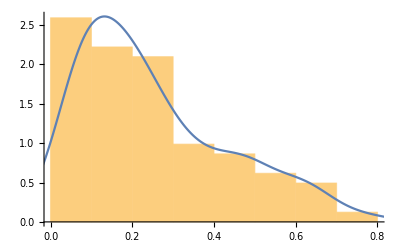

```mathematica
Show[{Histogram[nΔxyz, Automatic, "PDF"], SmoothHistogram[nΔxyz, Automatic, "PDF"]}]
```

Fig. 1 Error distribution of  coordinate vectors in case of all data

Let us consider now the error statistics of  the inliers only

```mathematica
XYZxyz=Transpose[trimmeddata];
```

```mathematica
Dimensions[XYZxyz]
```

{2,55,3}

```mathematica
nΔxyz=Map[Norm[#]&,XYZxyz[[2]]-Map[r1 r3.#+r2&,XYZxyz[[1]]]];
```

```mathematica
Mean[nΔxyz]
```

0.153311

```mathematica
StandardDeviation[nΔxyz]
```

0.0851091

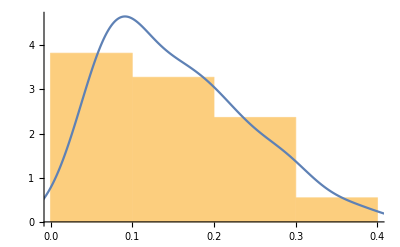

```mathematica
Show[{Histogram[nΔxyz, Automatic, "PDF"], SmoothHistogram[nΔxyz, Automatic, "PDF"]}]
```

Fig.2 Error distribution of  coordinate vectors in case of inliers only

## Conclusions

These results show that selecting  55 data points from the 81 ones could improve the results very considerably. In addition the hump in Fig.1 indicates a mixed distribution resulted by  the mixture of the outliers and inliers errors. The main advantage of this suggested technique comparing to the other non-iterative methods is that neither SVD nor tedious algebraic preprocessing is required. The efficiency of the method can be improved to parallelize the RANSAC computation, too.

## References

Awange J L, Grafarend E W, Paláncz B and Zaletnyik P (2010) Algebraic Geodesy and Geoinformatics 2nd Edition, Springer, Heidelberg.
 
Kenwright B (2012) Dual - Quaternions, From Classical  Mechanics to Computer Graphics and Beyond, pp.1 - 11.

 Paláncz B and Zaletnyik P (2011)  A symbolic solution of 3D affine transformation problem, The Mathematica Journal, Vol.13, pp. 1-15.
 
Proskova J (2011) Application of dual quaternions algorithm for geodetic datum transformation, Journal of Applied Mathematics, Vol. IV, No. 2., pp. 225 - 235

Sjöberg L E (2013) Closed -form and iterative weighted least squares solutions of Helmert transformation parameters, J of Geodetic Science, pp. 7-11.

Wang Yo, Wang Yu, Wu K, Yang H and Zhang H (2014)  A dual quaternion based, closed form pairwise registration algorithm for point clouds, ISPRS Journal of Photogrammetry and Remote Sensing, 94, pp. 63 - 69

Yaniv Z (2010) Random Sample Consensus (RANSAC) Algorithm, A Generic Implementation, Georgetown University Medical Center, Washington, DC, USA, zivy@isis.georgetown.edu

Zuliani M (2012) RANSAC for Dummies, vision.ece.ucsb.edu/~zuliani